```mathematica
Clear["Global`*"]
```

```mathematica
grr={y''[x]+y'[x]-2 y[x]==0,y[0]==4,y'[0]==-5}
out=DSolve[grr,y,x]
Simplify[grr/.out]
```

{-2 y[x]+y'[x]+y''[x]==0,y[0]==4,y'[0]==-5}

{{y→Function[{x},ⅇ^(-2 x) (3+ⅇ^(3 x))]}}

{{True,True,True}}

The above (example 2, p. 55) demonstrates that Mathematica can solve Homogeneous Linear ODEs with Constant Coefficients without the (manual) step of performing root solving.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+6 y'[x]+9 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-3 x) C[1]+ⅇ^(-3 x) x C[2]]}}

The above (example 3, p. 56) shows that Mathematica can find sol’n to another HLOCC without showing the characteristic equation, without constructing a basis.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y''[x]+9.04 y[x]+0.4 y'[x]==0,y[0]==0,y'[0]==3},y,x]
```

{{y→Function[{x},1. ⅇ^(-0.2 x) Sin[3. x]]}}

The above (example 5, p. 57) shows sol’n to eqn with complex roots, and with no special steps.

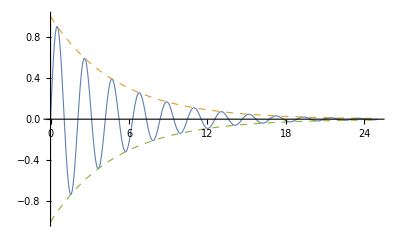

```mathematica
Plot[{ⅇ^(-0.2 x) Sin[3. x],ⅇ^(-0.2 x),-ⅇ^(-0.2 x)},{x,0,25},PlotRange->All,PlotStyle->{{Thickness[0.002]},{Dashed,Thickness[0.002]},{Dashed,Thickness[0.002]}}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Series[e^(ⅈ t),{t,0,10}]
```

1+ⅈ Log[e] t-1/2 Log[e]^2 t^2-1/6 ⅈ Log[e]^3 t^3+1/24 Log[e]^4 t^4+1/120 ⅈ Log[e]^5 t^5-1/720 Log[e]^6 t^6-(ⅈ Log[e]^7 t^7)/5040+(Log[e]^8 t^8)/40320+(ⅈ Log[e]^9 t^9)/362880-(Log[e]^10 t^10)/3628800+O[t]^11

```mathematica
%/.Log[e]->1
```

1+ⅈ t-t^2/2-(ⅈ t^3)/6+t^4/24+(ⅈ t^5)/120-t^6/720-(ⅈ t^7)/5040+t^8/40320+(ⅈ t^9)/362880-t^10/3628800+O[t]^11

1 - 15 General solution
Find a general solution. Check your answer by substitution. ODEs of this kind have important applications to be discussed in sections 2.4, 2.7, and 2.9.

1.  4 y'' - 25 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[4 y''[x]-25 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(5 x/2) C[1]+ⅇ^(-5 x/2) C[2]]}}

Answer above is correct.

3.  y'' + 6 y' + 8.96 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+6 y'[x]+8.96 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-3.2 x) C[1]+ⅇ^(-2.8 x) C[2]]}}

Answer above is correct.

5.  y'' + 2 π y' + π^2 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+2 π y'[x]+π^2 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-π x) C[1]+ⅇ^(-π x) x C[2]]}}

Answer above is correct.

7.  y'' + 4.5 y' = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+4.5 y'[x]==0,y,x]
```

{{y→Function[{x},-0.222222 ⅇ^(-4.5 x) C[1]+C[2]]}}

Answer above is correct, ( the constant coefficient C[1] was consolidated in the text answer, making the 2’s factor disappear).

9.  y'' + 1.8 y' - 2.08 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+1.8 y'[x]-2.08 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-2.6 x) C[1]+ⅇ^(0.8 x) C[2]]}}

Above answer is correct.

11. 4 y'' -4 y'  - 3 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[4 y''[x]-4 y'[x]-3 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-x/2) C[1]+ⅇ^(3 x/2) C[2]]}}

Answer above is correct.

13.  9 y'' - 30 y' + 25 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[9 y''[x]-30 y'[x]+25 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(5 x/3) C[1]+ⅇ^(5 x/3) x C[2]]}}

Answer above is correct.

15.  y'' + 0.54 y' + (0.0729 + π) y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+0.54 y'[x]+(0.0729+π) y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(-0.27 x) C[2] Cos[1.77245 x]+ⅇ^(-0.27 x) C[1] Sin[1.77245 x]]}}

```mathematica
(1.7724538509055159)^2
```

3.14159

The above answer is correct.

16 - 20 Find an ODE
y'' + a y' + b y = 0 for the given basis.

17.  ⅇ^(-√(5 x)), x ⅇ^(-√(5 x))

```mathematica
Clear["Global`*"]
```

```mathematica
h[x_]:=ⅇ^(-√5 x)
h'[x]
```

-√5 ⅇ^(-√5 x)

```mathematica
h''[x]
```

5 ⅇ^(-√5 x)

```mathematica
j[x_]:=x ⅇ^(-√5 x)
```

```mathematica
j'[x]
```

ⅇ^(-√5 x)-√5 ⅇ^(-√5 x) x

```mathematica
j''[x]
```

-2 √5 ⅇ^(-√5 x)+5 ⅇ^(-√5 x) x

```mathematica
Solve[h''[x]+a h'[x]+b h[x]==0&&j''[x]+a j'[x]+b j[x]==0,{a,b}]
```

{{a→2 √5,b→5}}

The above answer is correct.

19.  ⅇ^((-2+ⅈ)x), ⅇ^((-2-ⅈ)x)

```mathematica
Clear["Global`*"]
```

```mathematica
k[x_]:=ⅇ^((-2+ⅈ)x)
```

```mathematica
m[x_]:=ⅇ^((-2-ⅈ)x)
```

```mathematica
Solve[k''[x]+a k'[x]+b k[x]==0&&m''[x]+a m'[x]+b m[x]==0,{a,b}]
```

{{a→4,b→5}}

The above answer is correct.

21 - 30 Initial value problems
Solve the IVP. Check that your answer satisfies the ODE as well as the initial conditions.

21.  y'' +25 y = 0, y(0) = 4.6, y'(0) = -1.2

```mathematica
Clear["Global`*"]
```

```mathematica
arkosa={y''[x]+25 y[x]==0,y[0]==4.6,y'[0]==-1.2}
hap=DSolve[arkosa,y,x]
```

{25 y[x]+y''[x]==0,y[0]==4.6,y'[0]==-1.2}

{{y→Function[{x},4.6 Cos[5 x]-0.24 Sin[5 x]]}}

```mathematica
Simplify[arkosa/.hap]
```

{{Cos[5 x]==0,True,True}}

The above line indicates that Mathematica tested the initial value points and found that the sol’n worked correctly at those points.

```mathematica
r[x_]:=4.6 Cos[5 x]-0.24 Sin[5 x]
```

```mathematica
Simplify[r''[x]+25 r[x]]
```

-1.42109×10^-14 Cos[5 x]

What the above line seems to indicate is that, within default working precision, the answer is correct.

23.  y'' + y' -6 y = 0, y(0) = 10, y'(0) = 0

```mathematica
Clear["Global`*"]
```

```mathematica
redondo={y''[x]+y'[x]-6 y[x]==0,y[0]==10,y'[0]==0}
ghent=DSolve[redondo,y,x]
```

{-6 y[x]+y'[x]+y''[x]==0,y[0]==10,y'[0]==0}

{{y→Function[{x},2 ⅇ^(-3 x) (2+3 ⅇ^(5 x))]}}

```mathematica
Simplify[redondo/.ghent]
```

{{True,True,True}}

```mathematica
Simplify[2 ⅇ^(-3 x) (2+3 ⅇ^(5 x))]
```

ⅇ^(-3 x) (4+6 ⅇ^(5 x))

The above answer is correct; Mathematica tested both the initial value points as well as the general sol’n and found all sat.

25.  y'' - y = 0, y(0) = 2, y'(0) = -2

```mathematica
Clear["Global`*"]
```

```mathematica
treacle={y''[x]-y[x]==0,y[0]==2,y'[0]==-2}
rhet=DSolve[treacle,y,x]
```

{-y[x]+y''[x]==0,y[0]==2,y'[0]==-2}

{{y→Function[{x},2 ⅇ^-x]}}

```mathematica
Simplify[treacle/.rhet]
```

{{True,True,True}}

The above answer is correct; Mathematica tested both the initial value points as well as the general sol’n and found all sat.

27.  The ODE in problem 5, y(0) = 4.5, y'(0) = -4.5 π - 1 = 13.137

```mathematica
Clear["Global`*"]
```

```mathematica
jam={y''[x]+2π y'[x]+π^2 y[x]==0,y[0]==4.5,y'[0]==-4.5 π-1}
blank=DSolve[jam,y,x]
```

{π^2 y[x]+2 π y'[x]+y''[x]==0,y[0]==4.5,y'[0]==-15.1372}

{{y→Function[{x},-1. ⅇ^(-π x) (-4.5+1. x)]}}

```mathematica
rodz=blank[[1,1,2,2]]
```

-1. ⅇ^(-π x) (-4.5+1. x)

```mathematica
Expand[rodz]
```

4.5 ⅇ^(-π x)-1. ⅇ^(-π x) x

```mathematica
Simplify[jam/.blank]
```

{{ⅇ^(-π x)==0,True,True}}

```mathematica
TableForm[Table[Evaluate[rodz[x],{x,8}]]]
```

0.151249[1]
0.00466861[2]
0.000121049[3]
1.74367×10^-6[4]
(-7.53509×10^-8)[5]
(-9.76862×10^-9)[6]
(-7.03567×10^-10)[7]
(-4.25654×10^-11)[8]

```mathematica
TableForm[Table[{x,rodz},{x,8}],TableHeadings->{{},{"x ","rodz value"}}]
```

| x  | rodz value
 | 1 | 0.151249
 | 2 | 0.00466861
 | 3 | 0.000121049
 | 4 | 1.74367×10^-6
 | 5 | -7.53509×10^-8
 | 6 | -9.76862×10^-9
 | 7 | -7.03567×10^-10
 | 8 | -4.25654×10^-11

The above expression I interpret to mean that if x>5, then ⅇ^(-π x)  is effectively zero, and thereafter the checking statement ⅇ^(-π x)==0 will be true. But this doesn’t seem very satisfactory.

```mathematica
mn[x_]:=4.5 ⅇ^(-π x)-1. ⅇ^(-π x) x
mn''[x]+2 π mn'[x]+π^2 mn[x]
```

50.6964 ⅇ^(-π x)-9.8696 ⅇ^(-π x) x+π^2 (4.5 ⅇ^(-π x)-1. ⅇ^(-π x) x)+2 π (-15.1372 ⅇ^(-π x)+3.14159 ⅇ^(-π x) x)

```mathematica
Simplify[%]
```

0.

Okay, that’s more like it. The text answer agrees by the way. And by the way, there is a slight mistake in the problem, because the 13.137 should have a minus sign.

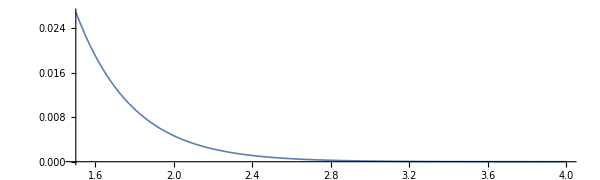

```mathematica
Plot[4.5 ⅇ^(-π x)-1. ⅇ^(-π x) x,{x,1.5,4},PlotRange->All,ImageSize->600,AspectRatio->0.3,PlotStyle->Thickness[0.002]]
```

29.  The ODE in problem 15, y(0) = 0, y'(0) = 1

```mathematica
Clear["Global`*"]
```

```mathematica
quil={y''[x]+0.54 y'[x]+(0.0729+π) y[x]==0,y[0]==0,y'[0]==1}
tig=DSolve[quil,y,x]
```

{3.21449 y[x]+0.54 y'[x]+y''[x]==0,y[0]==0,y'[0]==1}

{{y→Function[{x},0.56419 ⅇ^(-0.27 x) Sin[1.77245 x]]}}

```mathematica
Simplify[quil/.tig]
```

{{ⅇ^(-0.27 x) (-1.11022×10^-16 Cos[1.77245 x]+3.88578×10^-16 Sin[1.77245 x])==0,True,True}}

```mathematica
N[√π]
```

1.77245

```mathematica
1/%
```

0.56419

Checking these two quantities establishes that the answer agrees with the text’s. As for actually checking the answer, Mathematica has dodged the issue again.

```mathematica
fes[x_]:=1/(√π) ⅇ^(-0.27 x) Sin[√π x]
kres=Simplify[fes''[x]+0.54 fes'[x]+(0.0729+π) fes[x]]
```

2.22045×10^-16 ⅇ^(-0.27 x) Sin[√π x]

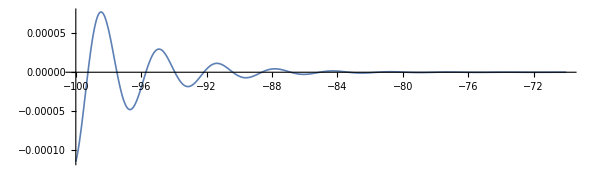

```mathematica
Plot[2.220446049250313*^-16 ⅇ^(-0.27 x) Sin[√π x],{x,-100,-70},PlotRange->All,ImageSize->600,AspectRatio->0.3,PlotStyle->Thickness[0.002]]
```

```mathematica
TableForm[Table[{x,fes[x]},{x,-100,100,20}],TableHeadings->{{},{"x ","func value"}}]
```

| x  | func value
 | -100 | -2.905×10^11
 | -80 | 5.58566×10^8
 | -60 | 2.75639×10^6
 | -40 | -27036.
 | -20 | 97.1904
 | 0 | 0.
 | 20 | -0.00198264
 | 40 | 0.0000112507
 | 60 | -2.33991×10^-8
 | 80 | -9.67281×10^-11
 | 100 | 1.02623×10^-12

I really can’t blame Mathematica for not being ready to say this is equal to zero. The text answer was achieved, that is something.

31 - 36 Linear independence is of basic importance, in this chapter, in connection with general solutions, as explained in the text. Are the following functions linearly independent on the given interval?

31.  ⅇ^(k x), x ⅇ^(k x), any interval

```mathematica
Clear["Global`*"]
```

```mathematica
r=FullSimplify[Solve[a ⅇ^(k x)==x ⅇ^(k x),a]]
```

{{a→x}}

A sol’n for a  has been found, but the sol’n says a is not a constant. Therefore the functions must be linearly independent. Answer agrees with text’s.

33.  x^2, x^2 Log[x], x > 1

```mathematica
Clear["Global`*"]
```

```mathematica
r=FullSimplify[Solve[a x^2==x^2 Log[x],a]]
```

{{a→Log[x]}}

Again, the functions must be independent, because the connecting factor is not constant. (Text agrees.)

35.  Sin[2 x], Cos[x] Sin[x], x < 0

```mathematica
Clear["Global`*"]
```

```mathematica
r=FullSimplify[Solve[a Sin[2 x]==Cos[x] Sin[x]&&x<0,a]]
```

{{a→ConditionalExpression[1/2,x<0]}}

Here Mathematica comes through by sniffing out a constant sol’n. This means that the two functions are linearly dependent.  (And the text agrees.)

37.  Instability. Solve y'' - y = 0 for the initial conditions y(0) = 1, y'(0) = -1. Then change the initial conditions to y(0) = 1.001, y'(0) = -0.999 and explain why this small change of 0.001 at t = 0 causes a large change later, e.g. 22 at t = 10. This is instability: a small initial difference in setting a quantity (a current, for instance) becomes larger and larger with time t. This is undesirable.

```mathematica
Clear["Global`*"]
```

```mathematica
hak={y''[t]-y[t]==0,y[0]==1,y'[0]==-1}
drak=DSolve[hak,y,t]
```

{-y[t]+y''[t]==0,y[0]==1,y'[0]==-1}

{{y→Function[{t},ⅇ^-t]}}

```mathematica
hur=drak[[1,1,2,2]]
```

ⅇ^-t

```mathematica
hak1={y''[t]-y[t]==0,y[0]==1.001,y'[0]==-0.999}
drak1=DSolve[hak1,y,t]
```

{-y[t]+y''[t]==0,y[0]==1.001,y'[0]==-0.999}

{{y→Function[{t},0.001 ⅇ^-t (1000.+1. ⅇ^(2 t))]}}

```mathematica
hur1=drak1[[1,1,2,2]]
```

0.001 ⅇ^-t (1000.+1. ⅇ^(2 t))

```mathematica
TableForm[Table[{t,N[hur,4],N[hur1,4]},{t,0,30,2}],TableHeadings->{{},{"t ","drak value ","drak1 value"}}]
```

| t  | drak value  | drak1 value
 | 0 | 1. | 1.001
 | 2 | 0.1353 | 0.142724
 | 4 | 0.01832 | 0.0729138
 | 6 | 0.002479 | 0.405908
 | 8 | 0.0003355 | 2.98129
 | 10 | 0.0000454 | 22.0265
 | 12 | 6.144×10^-6 | 162.755
 | 14 | 8.315×10^-7 | 1202.6
 | 16 | 1.125×10^-7 | 8886.11
 | 18 | 1.523×10^-8 | 65660.
 | 20 | 2.061×10^-9 | 485165.
 | 22 | 2.789×10^-10 | 3.58491×10^6
 | 24 | 3.775×10^-11 | 2.64891×10^7
 | 26 | 5.109×10^-12 | 1.9573×10^8
 | 28 | 6.914×10^-13 | 1.44626×10^9
 | 30 | 9.358×10^-14 | 1.06865×10^10

The table verifies what the text says, i.e. that there is a difference of 22 at t=10. And it gets much larger later.